```mathematica
(* Narrowband pulses with fixed profile bandwidths ϵ = 0.9, 0.8, 0.7, ... *)
(* Minimized total pulse area ≤ 5π *)
(* Target probability: p = 1, 1/2, 1/4 *)
(* Error < 10^-4 *)
```

```mathematica
plotUtils=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"plot_utils.m"}];
<<(plotUtils)
```

```mathematica
rootNB[cond_]:=Module[{x,left,right,step=0.005},
x=-1+step;While[cond[x],x+=step;left=x];
x=1-step;While[cond[x],x-=step;right=x];
{left-step/2,right+step/2}]
```

```mathematica
root=rootNB;
err=0.0001;
error=", error="<>ToString@err;
totalArea[rule_,npulses_]:=Module[{vars=rule/.Rule[a_,b_]->a},npulses Abs[vars[[-1]]/.rule]];
```

```mathematica
(*N=3 -- None found*)
```

```mathematica
(*N=4 -- None found*)
```

NB5; p=1, error=0.0001

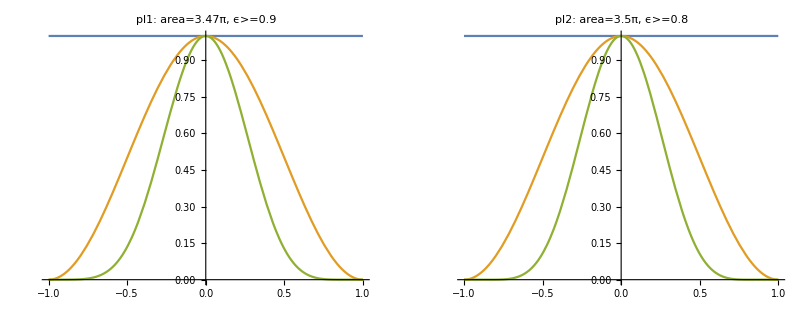

NB5; p=1/2, error=0.0001

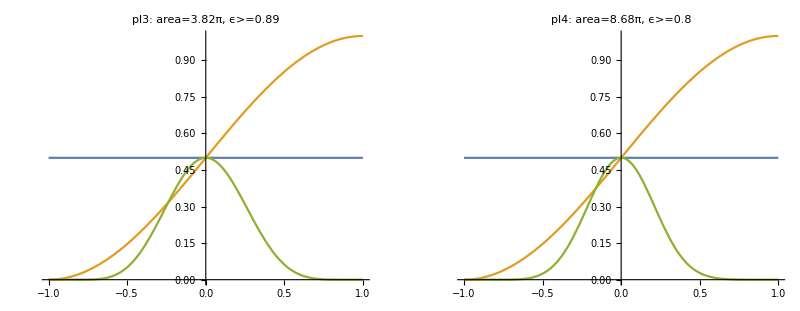

NB5; p=1/4, error=0.0001

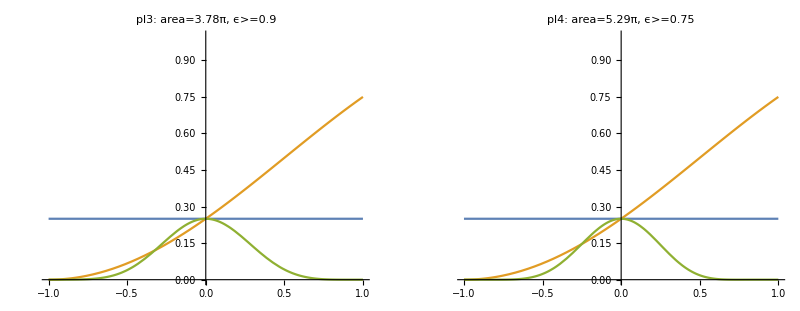

```mathematica
(*N=5*)
sequence=U[Δ1,Ω1].U[Δ2,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,0,label, totalArea[rule,5]]

pl1=plt[1.0,{Δ1->0.0834,Δ2->-1.0896,Δ3->6.7195,Ω1->0.6942},"pl1"];
pl2=plt[1.0,{Δ1->0.0796,Δ2->-1.0565,Δ3->6.6988,Ω1->0.7000},"pl2"];

pl3=plt[0.5,{Δ1->0.4489,Δ2->-1.3663,Δ3->11.0570,Ω1->0.7631},"pl3"];
pl4=plt[0.5,{Δ1->4.5277,Δ2->-2.0490,Δ3->20.8204,Ω1->1.7367},"pl4"];

pl5=plt[0.25,{Δ1->0.6536,Δ2->-1.5172,Δ3->7.1333,Ω1->0.7562},"pl3"];
pl6=plt[0.25,{Δ1->4.6016,Δ2->0.9305,Δ3->9.9641,Ω1->1.0574},"pl4"];

GGrid[Text[Style["NB5; p=1"<>error,FontSize->20]],{{pl1,pl2,Null,Null}},ImageSize->Full]
GGrid[Text[Style["NB5; p=1/2"<>error,FontSize->20]],{{pl3,pl4,Null,Null}},ImageSize->Full]
GGrid[Text[Style["NB5; p=1/4"<>error,FontSize->20]],{{pl5,pl6,Null,Null}},ImageSize->Full]
```

NB6; p=1, error=0.0001

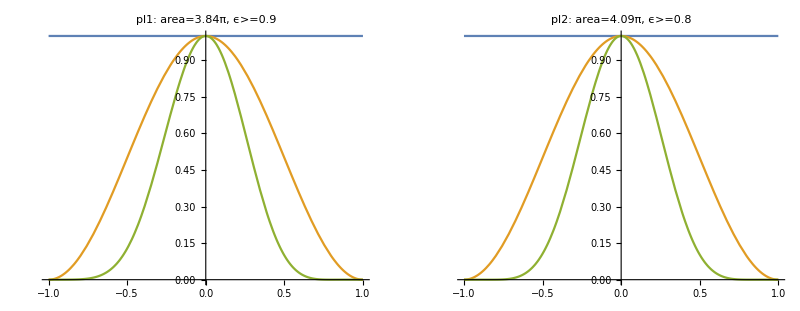

NB6; p=1/2, error=0.0001

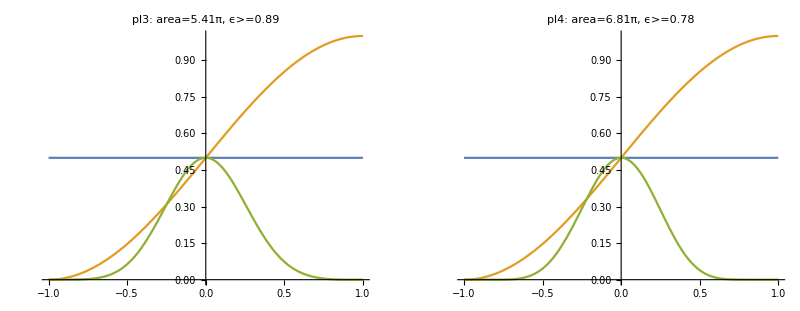

NB6; p=1/4, error=0.0001

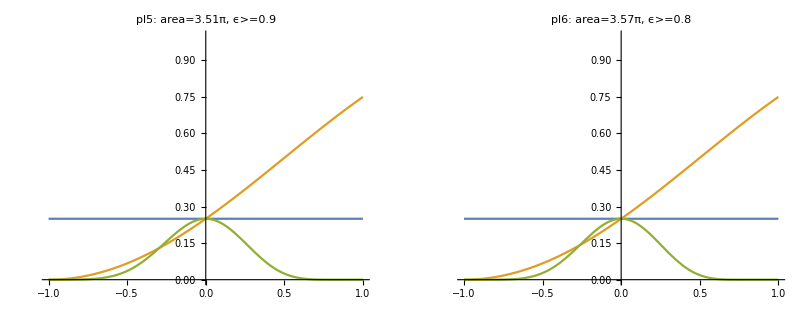

```mathematica
(*N=6 - Different Rabi N=5 provide smaller total area*)(*symmetric is better*)
sequenceS=U[Δ1,Ω1].U[Δ2,Ω1].U[Δ3,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltS[p_,rule_,label_]:=plot[p,err,sequenceS,rule,0,label,totalArea[rule,6]]

pl1=pltS[1.0,{Δ1->0.6748,Δ2->-2.3254,Δ3->0.6682,Ω1->0.6397},"pl1"];
pl2=pltS[1.0,{Δ1->0.072,Δ2->-0.9337,Δ3->5.2330,Ω1->0.6823},"pl2"];

pl3=pltS[0.50,{Δ1->0.4683,Δ2->1.6614,Δ3->-6.4231,Ω1->0.9023},"pl3"];
pl4=pltS[0.50,{Δ1->0.3038,Δ2->-8.2192,Δ3->6.5724,Ω1->1.1356},"pl4"];

pl5=pltS[0.25,{Δ1->0.3895,Δ2->0.8851,Δ3->-2.2763,Ω1->0.5853},"pl5"];
pl6=pltS[0.25,{Δ1->0.3828,Δ2->0.8594,Δ3->-2.2697,Ω1->0.5942},"pl6"];

GGrid[Text[Style["NB6; p=1"<>error,FontSize->20]],{{pl1,pl2,Null,Null}},ImageSize->Full]
GGrid[Text[Style["NB6; p=1/2"<>error,FontSize->20]],{{pl3,pl4,Null,Null}},ImageSize->Full]
GGrid[Text[Style["NB6; p=1/4"<>error,FontSize->20]],{{pl5,pl6,Null,Null}},ImageSize->Full]
```

NB7; p=1, error=0.0001

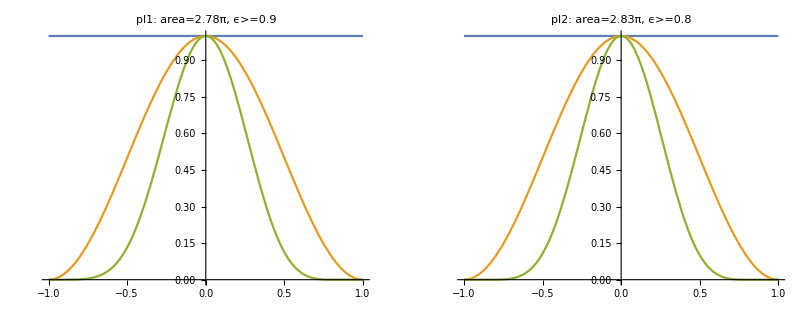

NB7; p=1/2, error=0.0001

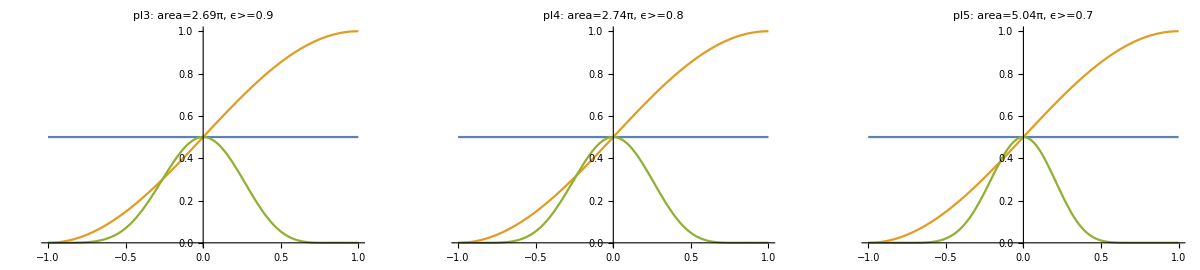

NB7; p=1/4, error=0.0001

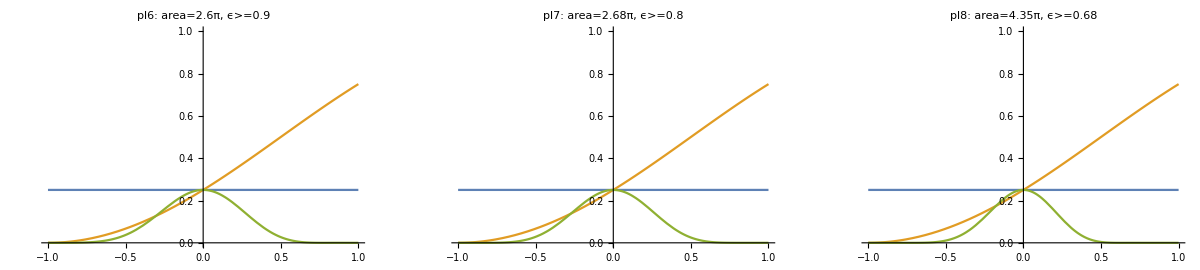

```mathematica
(*N=7 - Choose this*)
sequenceS=U[Δ1,Ω1].U[Δ2,Ω1].U[Δ3,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltS[p_,rule_,label_]:=plot[p,err,sequenceS,rule,0,label, totalArea[rule,7]]

pl1=pltS[1.0,{Δ1->0.7166,Δ2->-0.1185,Δ3->0.2727,Δ4->0.5910,Ω1->0.3967},"pl1"];
pl2=pltS[1.0,{Δ1->0.7207,Δ2->-0.1269,Δ3->0.2682,Δ4->0.5699,Ω1->0.4036},"pl2"];

pl3=pltS[0.50,{Δ1->0.0807,Δ2->0.3045,Δ3->0.7847,Δ4->-0.6154,Ω1->0.3849},"pl3"];
pl4=pltS[0.50,{Δ1->0.0377,Δ2->-0.3007,Δ3->0.2544,Δ4->-1.1804,Ω1->0.3910},"pl4"];
pl5=pltS[0.50,{Δ1->2.7101,Δ2->0.6501,Δ3->0.7199,Δ4->0.3204,Ω1->0.7206},"pl5"];

pl6=pltS[0.25,{Δ1->-0.2215,Δ2->-0.3498,Δ3->0.9019,Δ4->0.0639,Ω1->0.3719},"pl6"];
pl7=pltS[0.25,{Δ1->0.8788,Δ2->0.1052,Δ3->0.3760,Δ4->0.2930,Ω1->0.3823},"pl7"];
pl8=pltS[0.25,{Δ1->0.3759,Δ2->0.8892,Δ3->0.6388,Δ4->-2.9105,Ω1->0.6215},"pl8"];

GGrid[Text[Style["NB7; p=1"<>error,FontSize->20]],{{pl1,pl2,Null,Null}},ImageSize->Full]
GGrid[Text[Style["NB7; p=1/2"<>error,FontSize->20]],{{pl3,pl4,pl5,Null}},ImageSize->Full]
GGrid[Text[Style["NB7; p=1/4"<>error,FontSize->20]],{{pl6,pl7,pl8,Null}},ImageSize->Full]
```